ΛCDM model 
Ωmn :--->Ω_m^0
Ωdn :--->Ω_d^0
Em  :---->H^2/H_0^2

```mathematica
Em[x_]:=Ωmn ⅇ^(-3 x)+(1-Ωmn) ⅇ^(-3(1+w)x);
dEm[x_]:=D[Em[x],x];
w=-1;
{dEm[x]}
{Em[x]}
```

{-3 ⅇ^(-3 x) Ωmn}

{1-Ωmn+ⅇ^(-3 x) Ωmn}

```mathematica
Eqs:=F''[x]+(dEm[x]/(2Em[x])-1)F'[x]+dEm[x]/Em[x] F[x]+(3Ωmn ⅇ^(-3 x))/Em[x]==0;
Simplify[DSolve[Eqs,F[x],x]]
```

{{F[x]→1+(ⅇ^(3 x))^(1/12 (5-√73)) (1-Ωmn)^(1/12 (5-√73)) Ωmn^(1/12 (-5+√73)) C[1] Hypergeometric2F1[1/12 (1-√73),1/12 (5-√73),1-(√73)/6,(ⅇ^(3 x) (-1+Ωmn))/Ωmn]+(ⅇ^(3 x))^(1/12 (5+√73)) (1-Ωmn)^(1/12 (5+√73)) Ωmn^(1/12 (-5-√73)) C[2] Hypergeometric2F1[1/12 (1+√73),1/12 (5+√73),1/6 (6+√73),(ⅇ^(3 x) (-1+Ωmn))/Ωmn]}}

```mathematica
Ft[x_]:=1+(ⅇ^(3 x))^(1/12 (5+√73)) (1-Ωmn)^(1/12 (5+√73)) Ωmn^(1/12 (-5-√73)) C[2] Hypergeometric2F1[1/12 (1+√73),1/12 (5+√73),1/6 (6+√73),(ⅇ^(3 x) (-1+Ωmn))/Ωmn];
```

```mathematica
Ftt[R_]:=Ft[x]/.ⅇ^(3 x)->-(3Ωmn)/(-R+12-12Ωmn);
{Ftt[R]}
```

{1+3^(1/12 (5+√73)) (1-Ωmn)^(1/12 (5+√73)) Ωmn^(1/12 (-5-√73)) (-Ωmn/(12-R-12 Ωmn))^(1/12 (5+√73)) C[2] Hypergeometric2F1[1/12 (1+√73),1/12 (5+√73),1/6 (6+√73),-(3 (-1+Ωmn))/(12-R-12 Ωmn)]}

```mathematica
Fttt[z_]:=Ftt[R]/.R->12-12Ωmn+(3Ωmn-3)/z;
{Simplify[Fttt[z]]}
dRdz[z_]=-(3Ωmn-3)/z^2;
```

{1+(1-Ωmn)^(1/12 (5+√73)) Ωmn^(1/12 (-5-√73)) ((z Ωmn)/(-1+Ωmn))^(1/12 (5+√73)) C[2] Hypergeometric2F1[1/12 (1+√73),1/12 (5+√73),1/6 (6+√73),z]}

```mathematica
ft[z_]:=∫Fttt[z]dRdz[z]ⅆz;
{ft[z]}
```

{(3 (-1+Ωmn) Ωmn^(1/12 (-5-√73)+1/12 (5+√73)))/z-1/(z Gamma[1/12 (5+√73)])3 (1-Ωmn)^(1/12 (5+√73)) (-1+Ωmn) Ωmn^(1/12 (-5-√73)) ((z Ωmn)/(-1+Ωmn))^(1/12 (5+√73)) C[2] Gamma[1/12 (-7+√73)] HypergeometricPFQ[{-7/12+(√73)/12,1/12+(√73)/12},{1+(√73)/6},z]}

```mathematica
ftt[z_]:=(3 (-1+Ωmn))/z-1/(z Gamma[1/12 (5+√73)])3 (1-Ωmn)^(1/12 (5+√73)) (-1+Ωmn) Ωmn^(1/12 (-5-√73)) ((z Ωmn)/(-1+Ωmn))^(1/12 (5+√73)) C[2] Gamma[1/12 (-7+√73)] HypergeometricPFQ[{-7/12+(√73)/12,1/12+(√73)/12},{1+(√73)/6},z];
f[R_]:=ftt[z]/.z->-(3(-1+Ωmn))/(-R+12-12 Ωmn);
{Simplify[f[R]]}
```

{1/Gamma[1/12 (5+√73)](R+12 (-1+Ωmn)) Ωmn^(1/12 (-5-√73)) (Ωmn^(1/12 (5+√73)) Gamma[1/12 (5+√73)]-(3-3 Ωmn)^(1/12 (5+√73)) (Ωmn/(R+12 (-1+Ωmn)))^(1/12 (5+√73)) C[2] Gamma[1/12 (-7+√73)] HypergeometricPFQ[{-7/12+(√73)/12,1/12+(√73)/12},{1+(√73)/6},(3 (-1+Ωmn))/(R+12 (-1+Ωmn))])}

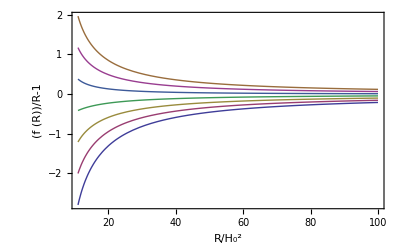

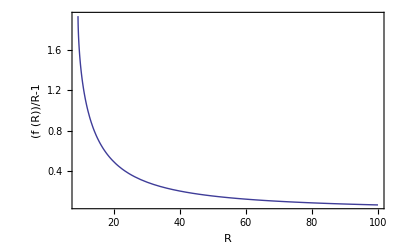

```mathematica
frg[R_,Dc_]:=-R +6 (1-Ωmn)+(R+12 (-1+Ωmn)) (1-Ωmn^(1/12 (-5-√73))(1-1 Ωmn)^(1/12 (5+√73)) ((3Ωmn)/(R+12 (-1+Ωmn)))^(1/12 (5+√73)) Dc 1/Gamma[1/12 (5+√73)] Gamma[1/12 (-7+√73)] Hypergeometric2F1[-7/12+(√73)/12,1/12+(√73)/12,1+(√73)/6,(3 (-1+Ωmn))/(R+12 (-1+Ωmn))])
Ωmn=0.24;
fig=Plot[{frg[R,1.5]/R,frg[R,1]/R,frg[R,0.5]/R,frg[R,0]/R,frg[R,-0.5]/R,frg[R,-1]/R,frg[R,-1.5]/R},{R,11,100},FrameLabel->{Style["R/H_0^2",14],Style["(f (R))/R-1",14]},Frame->True,PlotRange->All,RotateLabel->False]
Plot[{frg[R,-1]/R},{R,5,100},FrameLabel->{Style["R",14],Style["(f (R))/R-1",14]},Frame->True,PlotRange->All,RotateLabel->False]
```

```mathematica
Export["fr.eps",fig]
```

fr.eps

```mathematica
Dc=-1;
Frgt[x_]:=1+(ⅇ^(3 x))^(1/12 (5+√73)) (1-Ωmn)^(1/12 (5+√73)) Ωmn^(1/12 (-5-√73)) Dc Hypergeometric2F1[1/12 (1+√73),1/12 (5+√73),1/6 (6+√73),(ⅇ^(3 x) (-1+Ωmn))/Ωmn];
frgtt[R_]:=1/Gamma[1/12 (5+√73)](R+12 (-1+Ωmn)) Ωmn^(1/12 (-5-√73)) (Ωmn^(1/12 (5+√73)) Gamma[1/12 (5+√73)]-(3-3 Ωmn)^(1/12 (5+√73)) (Ωmn/(R+12 (-1+Ωmn)))^(1/12 (5+√73)) Dc Gamma[1/12 (-7+√73)] Hypergeometric2F1[-7/12+(√73)/12,1/12+(√73)/12,1+(√73)/6,(3 (-1+Ωmn))/(R+12 (-1+Ωmn))])
Subscript[N, 1]:=ϕ'[x]== -(Em'[x]/(2Em[x])-1)ϕ[x]-Em'[x]/Em[x] F[x]-(3Ωmn ⅇ^(-3x))/Em[x];
Subscript[N, 2] :=F'[x]==ϕ[x];
```

NDSolve::precw: The precision of the differential equation (« 1 ») is less than WorkingPrecision (35.).

{{F→InterpolatingFunction[{{-10.,0}},<>],ϕ→InterpolatingFunction[{{-10.,0}},<>]}}

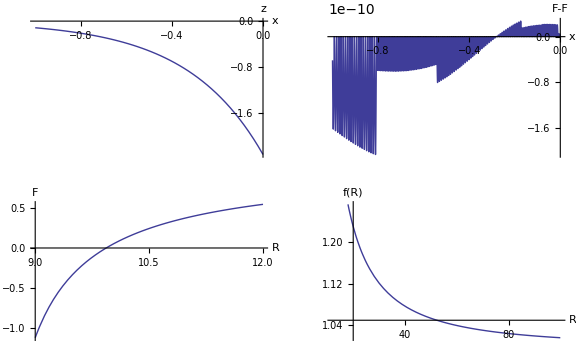

```mathematica
R[x_]:= 3(4Em[x]+Em'[x]);
fRR[x_]:=F'[x]/R'[x];
M2[x_]:=1/3(F[x]/fRR[x]-R[x]);
s1=NDSolve[{Subscript[N, 1],Subscript[N, 2],ϕ[-3]==Frgt'[-3],F[-3]==Frgt[-3]},{F,ϕ},{x,  -10,0},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35,MaxSteps->Infinity]
GraphicsGrid[{ {Plot[Evaluate[(ⅇ^(3 x) (-1+Ωmn))/Ωmn/.s1],{x, -1,0},AxesLabel->{"x","z"}],Plot[Evaluate[Frgt[x]-F[x]/.s1],{x, -1,0},AxesLabel->{"x","F-F"}]},
 {Plot[Evaluate[frgtt'[R]/.s1],{R, 9,12},AxesLabel->{"R","F"}],Plot[Evaluate[frgtt[R]/R/.s1],{R, 12,100},AxesLabel->{"R","f(R)"}]}
},ImageSize->Large]
```